```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
f[x_,a1_,a2_,a3_,a4_]:=a1  + a2 x + a3 x^2 + a4 x^4
```

```mathematica
fSolve[a1_,a3_]:=Block[{sol=NSolve[{f[1,a1,a,a3,b]==1,f[2,a1,a,a3,b]==3},{a,b}]},sol[[1,All,2]]]
fSolver[a1_,a3_]:=Block[{sol=fSolve[a1,a3]},f[x,a1,sol[[1]],a3,sol[[2]]]]
```

```mathematica
sol1=fSolver[1,2];
sol2=fSolver[0,1];
sol3=fSolver[-3,1];
sol4=fSolver[3,1];
```

```mathematica
Needs["PolygonPlotMarkers`"]

allShapes=PolygonMarker[All]
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,1]},ImageSize->30,PlotRange->1.5,PlotRangePadding->0,ImagePadding->0],#]&/@allShapes
```

{TripleCross,Y,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarThick,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,EightfoldCross,Disk,H,I,N,Z,S,Sw,Sl}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

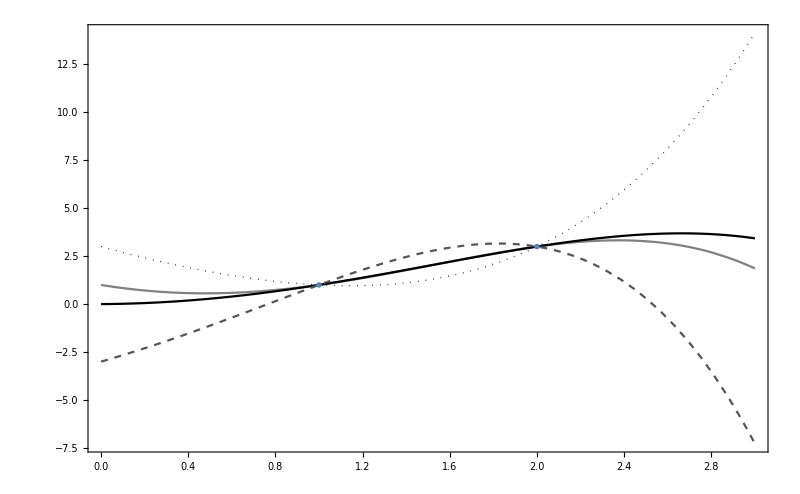

```mathematica
Show[Plot[{sol1,sol2,sol3,sol4},{x,0,3},Axes->None,PlotStyle->{Gray,Black,Directive[Darker@Gray,Dashed],Directive[Black,Dotted,Thick]},PlotRange->Full,FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False},PlotStyle->"Brighband}1"],ListPlot[{{1,1},{2,3}},PlotMarkers->Graphics[{FaceForm[Blue],PolygonMarker[ToString@"Disk",Scaled[0.04]]},AlignmentPoint->{0,0}]]]
```